```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 8/ohg6-hw8/";
(*~ Windows ~*)
(*main="/Users/Mikhail/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/ohg6-hw4/";*)

SetDirectory[main];
$Line=0;
```

## 1

```mathematica
data=Import["1/hw8-1.txt","Data"];
```

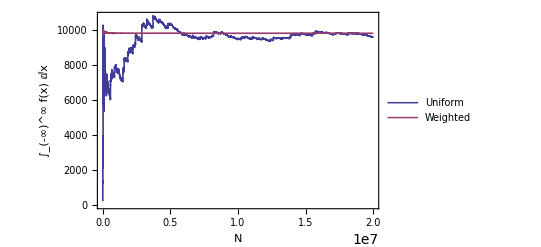

1/integ.png

```mathematica
ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]]},Frame->True,Axes->False,FrameTicks->{{Automatic,False},{Automatic,False}},PlotLegends->{"Uniform","Weighted"},PlotStyle->Thickness[0.003],PlotRange->{All,All},GridLines->{None,{(2π)^5}},FrameLabel->{"N","∫_(-∞)^∞  f(x) ⅆx"},PlotTheme->"Classic",BaseStyle->{FontSize->12},ImageSize->400]
Export["1/integ.png",%]
```

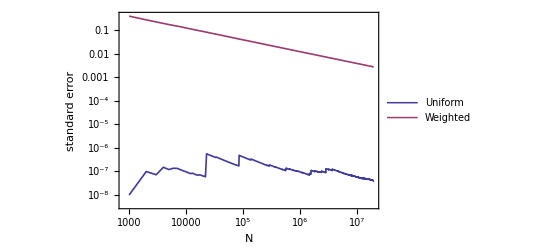

1/stderr.png

```mathematica
ListLogLogPlot[{data[[All,{1,4}]],data[[All,{1,5}]]},Joined->True,Frame->True,Axes->False,FrameTicks->{{Automatic,False},{Automatic,False}},PlotLegends->{"Uniform","Weighted"},PlotStyle->Thickness[0.003],PlotRange->{All,All},FrameLabel->{"N","standard error"},PlotTheme->"Classic",BaseStyle->{FontSize->12},ImageSize->400]
Export["1/stderr.png",%]
```

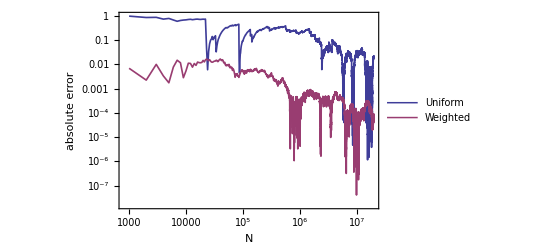

1/abserr.png

```mathematica
ListLogLogPlot[{data[[All,{1,6}]],data[[All,{1,7}]]},Joined->True,Frame->True,Axes->False,FrameTicks->{{Automatic,False},{Automatic,False}},PlotLegends->{"Uniform","Weighted"},PlotStyle->Thickness[0.003],PlotRange->{All,All},FrameLabel->{"N","absolute error"},PlotTheme->"Classic",BaseStyle->{FontSize->12},ImageSize->400]
Export["1/abserr.png",%]
```

## 2

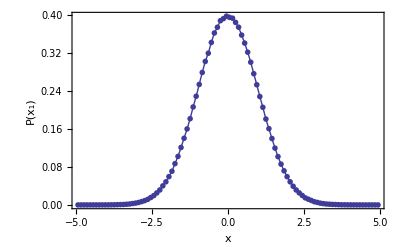

2/prob.png

```mathematica
data2gauss=Import["2/gauss.txt","Data"];
Show[ListPlot[data2gauss,PlotRange->All,PlotStyle->PointSize[0.01],PlotTheme->"Classic"],ListLinePlot[data2gauss,PlotTheme->"Classic"],Frame->True,Axes->False,FrameTicks->{{Automatic,False},{Automatic,False}},FrameLabel->{"x","P(x_1)"},BaseStyle->{FontSize->12},ImageSize->400]
Export["2/prob.png",%]
```